```mathematica
Load["MH0","MH1"];
sbone=ImportGray["M1/bone_small.png"];
```

Testing 1

```mathematica
morphoDynamic[threshold[sbone,0.5]]
```

Testing 2

```mathematica
showBinaryImageComponent[threshold[sbone,0.5]]
```

Testing 3

```mathematica
Manipulate[showGrayImage[labelComponents[threshold[sbone,v],object]⟦1⟧],{{v,0.5},0,.99},{object,{"2D8","2D4"}}]
```

Testing 4

```mathematica
showLargestComponents[sbone]
```

Problem 1

Part::partd: Part specification Missing[KeyAbsent,0]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Missing[KeyAbsent,0]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Missing[KeyAbsent,0]⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression 1+Missing[KeyAbsent,0]⟦1,1⟧ cannot be used as a part specification.

Part::pkspec1: The expression 1+Missing[KeyAbsent,0]⟦2,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

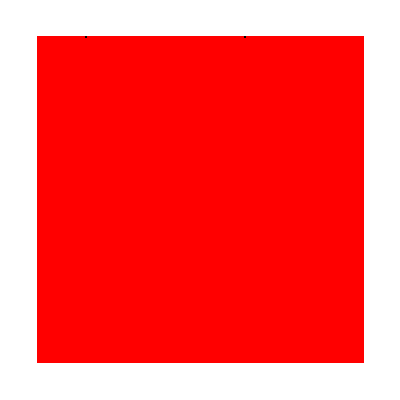

```mathematica
fillHoles[img_,conn_]:=flood[img,FirstPosition[img,0],conn]⟦1⟧/.{0->1,1->0};
imgLB=Reverse[ImportGray["M1/bone_large.png"]];
showGrayOverlay[
imgLB,
open[fillHoles[
maskComponents[
threshold[imgLB,.45],
0,{1,2}],
1]]]
```